# Turning rates from the data: calculate, and compare with single simulation case

```mathematica
allturnratedata=ParallelTable[Map[getturnrate[#,alldtused[[col]],antsizes[[col]]]&,alltrajcoords[[col]],{2}],{col,4}];
```

```mathematica
(* the parameters that set the behavior for this are:  turnspeeddecayrate=7, turnspeedsigma=5.  These variables were defined in file (0) *)
(* generate a single trajectory corresponding to each returning and potential forager *)
testsimtraj=Monitor[Table[
boundary=smoothedgedata[[col]];
speedavg=Mean[allspeeds[[col,group,ant]]]*antsizes[[col]];
dt=alldtused[[col]];
PTWant[alltrajcoords[[col,group,ant]],alltimes[[col,group,ant]],speedavg,turnspeeddecayrate,turnspeedsigma,{xmax,ymax},boundary,dt],
{col,4},{group,4},{ant,Length[alltimes[[col,group]]]}]
,{col,group,ant}];
allturnratesim=ParallelTable[Map[getturnrate[#,alldtused[[col]],antsizes[[col]]]&,testsimtraj[[col]],{2}],{col,4}];
```

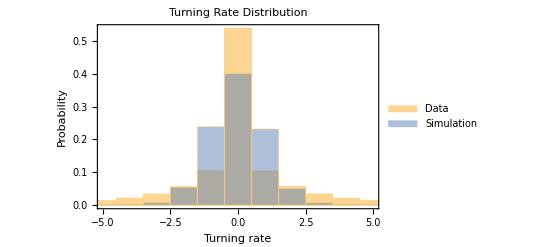

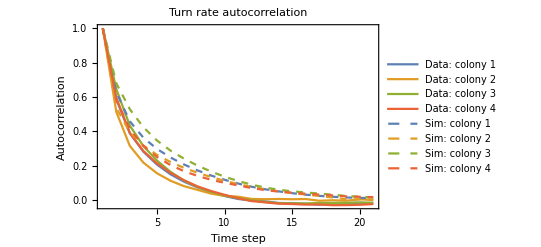

```mathematica
Histogram[{Flatten[allturnratedata],Flatten[allturnratesim]},{-5.5,5.5,1},"PDF",PlotRange->{{-5,5},Automatic},ChartLegends->{"Data","Simulation"},PlotRange->{{-5,5},Automatic},ChartLegends->{"Simulation"},Frame->True,FrameLabel->{"Turning rate","Probability"},PlotLabel->"Turning Rate Distribution"]

Show[ListPlot[CorrelationFunction[Flatten[#],{20}]&/@allturnratedata,Joined->True,PlotRange->All,PlotLabel->"Turn rate autocorrelation",Frame->True,FrameLabel->{"Time step","Autocorrelation"},PlotLegends->{"Data:  colony 1","Data:  colony 2","Data:  colony 3","Data:  colony 4"}],
ListPlot[CorrelationFunction[Flatten[#],{20}]&/@allturnratesim,PlotRange->All,PlotLabel->"Turn rate autocorrelation",PlotStyle->Dashed,Joined->True,PlotLegends->{"Sim:  colony 1","Sim:  colony 2","Sim:  colony 3","Sim:  colony 4"}]
]
```

# Generate simulated trajectories, and calculate surrounding density of ants NOTE: this code takes a while to run, and requires significant memory to store all trajectories

Simulated trajectories

```mathematica
numcases=50;  (* generate 50 trajectories for each returning and potential forager *)
allsimtraj=Monitor[Table[
Table[
boundary=smoothedgedata[[col]];
speedavg=Mean[allspeeds[[col,group,ant]]]*antsizes[[col]];
dt=alldtused[[col]];
PTWant[alltrajcoords[[col,group,ant]],alltimes[[col,group,ant]],speedavg,turnspeeddecayrate,turnspeedsigma,{xmax,ymax},boundary,dt],
numcases],
{col,4},{group,4},{ant,Length[alltimes[[col,group]]]}]
,{col,group,ant}];
```

Surrounding densities of ants

### Surrounding density of potential foragers

```mathematica
simdensityPF=Monitor[Table[
Module[{traj,distances,sz,individualcorrection},
traj={alltrajinterpolated[[col,group,ant]]ᵀ[[1]],allsimtraj[[col,group,ant,case]]}ᵀ;
distances=getdistances[#[[2]],TtrajpointsPF[[col,#[[1]]-alltrackingrange[[col,1]]+1]]]&/@traj;
sz=mult antsizes[[col]];
individualcorrection=0; (* because these are simulated trajectories *)
(gweights[[1]]*(Length[Select[#,0≤ #≤sz&]]-individualcorrection)
+gweights[[2]]*Length[Select[#,sz<#≤2sz&]]
gweights[[3]]*Length[Select[#,2sz<#≤3sz&]])&/@distances
]
,{col,4},{group,4},{ant,Length[alltrajinterpolated[[col,group]]]},{case,numcases}]
,{col,group,ant,case}];
```

### Surrounding density of returning foragers

```mathematica
simdensityRF=Monitor[Table[
Module[{traj,distances,sz,individualcorrection},
traj={alltrajinterpolated[[col,group,ant]]ᵀ[[1]],allsimtraj[[col,group,ant,case]]}ᵀ;
distances=getdistances[#[[2]],TtrajpointsRF[[col,#[[1]]-alltrackingrange[[col,1]]+1]]]&/@traj;
sz=mult antsizes[[col]];
individualcorrection=0; (* because these are simulated trajectories *)
(gweights[[1]]*(Length[Select[#,0≤ #≤sz&]]-individualcorrection)
+gweights[[2]]*Length[Select[#,sz<#≤2sz&]]
gweights[[3]]*Length[Select[#,2sz<#≤3sz&]])&/@distances
]
,{col,4},{group,4},{ant,Length[alltrajinterpolated[[col,group]]]},{case,numcases}]
,{col,group,ant,case}];
```

# Save results, to use in analysis and for making plots

```mathematica
Save[savedir<>"simdensityPF",simdensityPF]
Save[savedir<>"simdensityRF",simdensityRF]
```